## Single interval examples

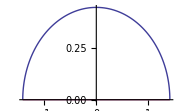

```mathematica
V[x_]:=x^2;
EquilibriumMeasure[V]
```

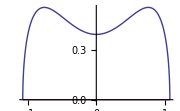

```mathematica
V[x_]:=x^4;
EquilibriumMeasure[V]
```

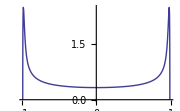

```mathematica
V[x_]:=x^100;
LinePlot[EquilibriumMeasure[V]]
```

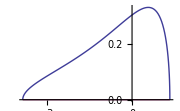

```mathematica
V[x_]:=Exp[x]-x;
EquilibriumMeasure[V]
```

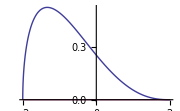

```mathematica
V[x_]:=x^2/5-4/15 x^3+x^4/20+8/5 x;
EquilibriumMeasure[V]
```

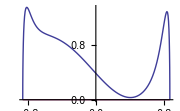

```mathematica
V[x_]:=Sin[3 x] + 10 x^20;
EquilibriumMeasure[V]
```

## Wishart example

```mathematica
V[x_]:=x-0.5 Log[x]
```

We need to specify an initial guess.  This also enforces that only a single interval of support will be considered

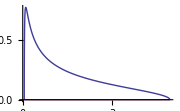

```mathematica
EquilibriumMeasure[V,{.01,1.}]
```

## Two interval example

The potential that we calculate ethe equilibrium measure, with different scalings

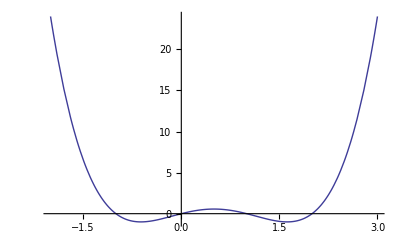

```mathematica
V[x_]:=x^4-2 x^3-x^2+2x;
Plot[V[x],{x,-2,3}]
```

For small scaling, the support is still a single interval

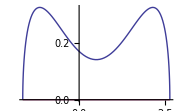

```mathematica
EquilibriumMeasure[.1V[#]&]
```

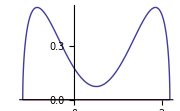

```mathematica
EquilibriumMeasure[.4V[#]&]
```

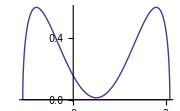

```mathematica
EquilibriumMeasure[.6V[#]&]
```

For large scaling, the support splits

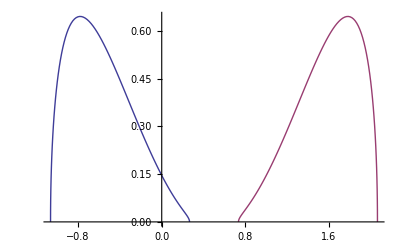

```mathematica
LinePlot[EquilibriumMeasure[.7V[#]&],PlotRange->All]
```

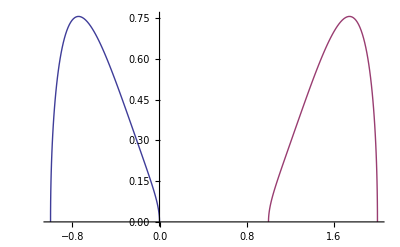

```mathematica
LinePlot[EquilibriumMeasure[V[#]&],PlotRange->All]
```

Warning: the algorithm may fail

```mathematica
EquilibriumMeasure[.5V[#]&]//Domain
```

Line[{-1.25,-1.25}]